## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="RPE";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_trp3.csv";

mainFolder = "fit_RPE_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{ru5p__D,Null,Keq substrate}

{3.9,Keq value}

{{{ru5p__D,Null}},kcat substrates}

{67000,kcat value}

{ru5p__D,Km or S05 substrate}

{0.0016,Km or S05 value}

{ru5p__D,Other parameter susbtrate}

{42000000,Other parameter value}

{{{ru5p__D,Null}},kcat substrates}

{30400,kcat value}

{ru5p__D,Km or S05 substrate}

{0.0018,Km or S05 value}

{ru5p__D,Other parameter susbtrate}

{17000000,Other parameter value}

{{{ru5p__D,Null}},kcat substrates}

{14700,kcat value}

{ru5p__D,Km or S05 substrate}

{0.0024,Km or S05 value}

{ru5p__D,Other parameter susbtrate}

{6000000,Other parameter value}

{{{ru5p__D,Null}},kcat substrates}

{1300,kcat value}

{ru5p__D,Km or S05 substrate}

{0.0048,Km or S05 value}

{ru5p__D,Other parameter susbtrate}

{200000,Other parameter value}

{{{ru5p__D,Null}},kcat substrates}

{500,kcat value}

{ru5p__D,Other parameter susbtrate}

{1500,Other parameter value}

{ru5p__D,Km or S05 substrate}

{0.0032,Km or S05 value}

{{{ru5p__D,Null}},kcat substrates}

{1600,kcat value}

{ru5p__D,Km or S05 substrate}

{0.0022,Km or S05 value}

{ru5p__D,Other parameter susbtrate}

{7100,Other parameter value}

{{{ru5p__D,Null}},kcat substrates}

{3800,kcat value}

{ru5p__D,Km or S05 substrate}

{0.0012,Km or S05 value}

{ru5p__D,Other parameter susbtrate}

{3200000,Other parameter value}

(ru5p__D^c⇌xu5p__D^c)^RPE

uni-uni;

Structure: 6

Active sites: 6

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ru5p__D,Null | 3.9 | 3.705
4.095 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ru5p__D | 0.0016 | 0.0014
0.0018 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0018 | 0.0017
0.0019 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0024 | 0.002
0.0028 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0048 | 0.0043
0.0053 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0032 | 0.0029
0.0035 |  | M | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | 0.0022 | 0.0019
0.0025 |  | M | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | 0.0012 | 0.0011
0.0013 |  | M | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ru5p__D | Null | 241652. | 213880.
264375. | 1/s | 8.5 | 37 | glygly | 0.05
dtpa | 0.005 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 109645. | 103514.
115777. | 1/s | 8.5 | 37 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 53019.2 | 49773.1
56265.3 | 1/s | 8.5 | 37 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 4688.77 | 4328.1
5049.45 | 1/s | 8.5 | 37 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 1501.41 | 1441.35
1561.46 | s^(-1) | 7.5 | 37 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | Null | 4804.5 | 4594.3
5014.69 | 1/s | 7.5 | 37 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | Null | 11410.7 | 10930.2
11891.1 | 1/s | 7.5 | 37 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | kcat/Km | ru5p__D | 42000000 | 3.99×10^7
4.41×10^7 |  | 1/(M*s) | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | kcat/Km | ru5p__D | 17000000 | 1.615×10^7
1.785×10^7 |  | 1/(M*s) | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | kcat/Km | ru5p__D | 6000000 | 5.7×10^6
6.3×10^6 |  | 1/(M*s) | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | kcat/Km | ru5p__D | 200000 | 190000.
210000. |  | 1/(M*s) | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | kcat/Km | ru5p__D | 1500 | 1425.
1575. |  | M^(-1)*s^(-1) | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | kcat/Km | ru5p__D | 7100 | 6745.
7455. |  | M^(-1)*s^(-1) | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | kcat/Km | ru5p__D | 3200000 | 3.04×10^6
3.36×10^6 |  | M^(-1)*s^(-1) | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1,1,1,1,1,1};
s05Priorities = Null;
kcatPriorities = {1,1,1,1,1,1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = {0,0,0,0,0,0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(ru5p__D^c⇌xu5p__D^c)^RPE

uni-uni;

Structure: 6

Active sites: 6

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ru5p__D,Null | 3.9 | 3.705
4.095 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ru5p__D | 0.0016 | 0.0014
0.0018 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0018 | 0.0017
0.0019 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0024 | 0.002
0.0028 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0048 | 0.0043
0.0053 |  | M | 8.5 | 23 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | 0.0032 | 0.0029
0.0035 |  | M | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | 0.0022 | 0.0019
0.0025 |  | M | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | 0.0012 | 0.0011
0.0013 |  | M | 7.5 | 25 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | ru5p__D | Null | 241652. | 213880.
264375. | 1/s | 8.5 | 37 | glygly | 0.05
dtpa | 0.005 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 109645. | 103514.
115777. | 1/s | 8.5 | 37 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 53019.2 | 49773.1
56265.3 | 1/s | 8.5 | 37 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 4688.77 | 4328.1
5049.45 | 1/s | 8.5 | 37 | glygly | 0.05 | mg2 | 0.0069
cl | 0.0138
1 | ru5p__D | Null | 1501.41 | 1441.35
1561.46 | s^(-1) | 7.5 | 37 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | Null | 4804.5 | 4594.3
5014.69 | 1/s | 7.5 | 37 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05
1 | ru5p__D | Null | 11410.7 | 10930.2
11891.1 | 1/s | 7.5 | 37 | hepes | 0.05 | mg2 | 0.01
cl | 0.02
na1 | 0.05

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_RPE[c] + ru5p__D[c] <=> E_RPE[c]&ru5p__D",
				"E_RPE[c]&ru5p__D <=> E_RPE[c]&xu5p__D",
				"E_RPE[c]&xu5p__D <=> E_RPE[c] + xu5p__D[c]"};



enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((RPE^c)_^+ru5p__D^c⇌(RPE^c&ru5p_^D)_^)^RPE1,((RPE^c&xu5p_^D)_^⇌(RPE^c)_^+xu5p__D^c)^RPE2,((RPE^c&ru5p_^D)_^⇌(RPE^c&xu5p_^D)_^)^RPE3}

```mathematica
Print[enzymeModel]
```

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((RPE^c)_^+ru5p__D^c⇌(RPE^c&ru5p_^D)_^)^RPE1,Overscript[(RPE^c&xu5p_^D)_^⇌(RPE^c)_^+xu5p__D^c, RPE2],((RPE^c&ru5p_^D)_^⇌(RPE^c&xu5p_^D)_^)^RPE3};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=6;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=300;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

{ru5p__D^c→0}

{xu5p__D^c→0}

{ru5p__D^c→∞}

{xu5p__D^c→∞}

Added inhibition reactions:

{}

Generating flux equation...

{((RPE^c&ru5p_^D)_^-((RPE^c&xu5p_^D)_^)/K_RPE3) Volume_c k_RPE3^⟶}

Volume_c (-(RPE^c&xu5p_^D)_^ k_RPE3^⟵+(RPE^c&ru5p_^D)_^ k_RPE3^⟶)

1

2

3

0.03016

4

0.0002

5

0.000085

Simplifying...

6

0.03136

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
Print[enzymeModel]
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
Print[bufferInfo]
```

{{{trishcl,Tris-HCl},8.14,1,0},{{tris,Tris},8.14,1,0},{{trisac,Tris-acetate},8.14,1,0},{{edta,EDTA},Null,Null,Null},{{tric,Tricine},8.07,0,-1},{{tricna,Tricine-Na},8.07,0,-1},{{hepesnaoh,Hepes-NaOH},7.5,0,-1},{{pipeskoh,PIPES-KOH},6.64,-1,-2},{{kpi,KPO4},6.88,-1,-2},{{napi,sodium phosphate},6.88,-1,-2},{{nakpi,Na+/K+ phosphate},6.88,-1,-2},{{chesk,CHES-K},9.37,0,-1},{{hepes,Hepes},7.5,0,-1},{{hepesbtp,HEPES-BTP},Null,Null,Null},{{pipes,Pipes},6.64,-1,-2},{{mops,MOPS},7.12,0,-1},{{mopsnaoh,MOPS/NaOH},7.12,0,-1},{{mopskoh,MOPS-KOH},7.12,0,-1},{{mes,MES},6.14,0,-1},{{netmphn,N-ethylmorpholine},7.83,1,0},{{detam,diethanolamine},8.95,1,0},{{glygly,glycylglycine},8.2,0,-1},{{imdzcl,imidazole-Cl},7.06,1,0},{{imdz_MIXED,mixed imidazoles},Null,Null,Null},{{24dmid,2,4-dimethylimidazole},Null,Null,Null},{{teoa,triethanolamine},7.83,1,0},{{teoahcl,triethanolamine-HCl},7.83,1,0},{{pi_buffer,Phosphoric acid},7.198,-1,-2},{{dtpa,DTPA},Null,Null,Null}}

```mathematica
FilePrint@dataPathList
```

Priority	ru5p__D[c]	xu5p__D[c]	param_RPE_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt"	3.9
1	0.0001600000000000001	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.09090909090909095
1	0.0002535829107937784	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.13680688860321014
1	0.00040190182904153293	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.2007600089131018
1	0.0006369714728855961	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.28474724895080156
1	0.0010095317511683093	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.386863179846857
1	0.001600000000000001	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.5000000000000001
1	0.002535829107937784	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.6131368201531432
1	0.004019018290415333	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7152527510491989
1	0.006369714728855961	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7992399910868984
1	0.010095317511683098	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.86319311139679
1	0.016000000000000007	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.9090909090909091
1	0.00017999999999999998	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.09090909090909091
1	0.0002852807746430005	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.13680688860321005
1	0.0004521395576717243	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.20076000891310172
1	0.0007165929069962951	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.2847472489508014
1	0.0011357232200643484	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.38686317984685714
1	0.0017999999999999997	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.4999999999999999
1	0.0028528077464300052	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.6131368201531432
1	0.004521395576717243	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7152527510491986
1	0.007165929069962951	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7992399910868982
1	0.011357232200643478	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.8631931113967901
1	0.018	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.9090909090909092
1	0.00023999999999999995	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.09090909090909091
1	0.0003803743661906673	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.13680688860321003
1	0.0006028527435622989	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.20076000891310167
1	0.0009554572093283933	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.2847472489508014
1	0.0015142976267524643	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.3868631798468571
1	0.0023999999999999994	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.5
1	0.003803743661906673	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.6131368201531432
1	0.00602852743562299	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7152527510491985
1	0.009554572093283933	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7992399910868982
1	0.015142976267524635	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.8631931113967899
1	0.023999999999999994	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.9090909090909091
1	0.00047999999999999996	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.09090909090909091
1	0.0007607487323813347	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.13680688860321005
1	0.001205705487124598	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.2007600089131017
1	0.001910914418656787	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.28474724895080145
1	0.003028595253504929	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.3868631798468571
1	0.0048	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.5
1	0.007607487323813347	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.6131368201531432
1	0.012057054871245986	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7152527510491987
1	0.01910914418656787	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7992399910868982
1	0.030285952535049277	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.86319311139679
1	0.047999999999999994	0	1	8.5	23	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.9090909090909091
1	0.00031999999999999986	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.09090909090909086
1	0.0005071658215875563	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.13680688860321
1	0.0008038036580830652	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.20076000891310164
1	0.001273942945771191	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.2847472489508014
1	0.002019063502336619	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.38686317984685703
1	0.003199999999999999	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.49999999999999983
1	0.005071658215875564	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.6131368201531431
1	0.008038036580830651	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7152527510491984
1	0.01273942945771191	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7992399910868981
1	0.02019063502336618	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.8631931113967899
1	0.03199999999999999	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.909090909090909
1	0.00021999999999999998	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.09090909090909088
1	0.00034867650234144505	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.13680688860321005
1	0.0005526150149321074	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.20076000891310167
1	0.000875835775217694	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.2847472489508014
1	0.0013881061578564257	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.3868631798468571
1	0.0021999999999999997	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.5
1	0.0034867650234144507	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.6131368201531431
1	0.005526150149321074	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7152527510491986
1	0.00875835775217694	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7992399910868981
1	0.01388106157856425	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.86319311139679
1	0.021999999999999995	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.9090909090909091
1	0.00011999999999999995	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.09090909090909088
1	0.00019018718309533363	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.13680688860321
1	0.0003014263717811494	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.20076000891310164
1	0.0004777286046641966	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.28474724895080133
1	0.0007571488133762321	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.38686317984685703
1	0.0011999999999999995	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.49999999999999994
1	0.0019018718309533362	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.613136820153143
1	0.0030142637178114944	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7152527510491984
1	0.004777286046641966	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.7992399910868982
1	0.007571488133762321	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.8631931113967899
1	0.011999999999999995	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt"	0.9090909090909092
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	241652.2342394583
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	109645.19284894825
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	53019.221542090105
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	8.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4688.774694198445
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	1501.4055424767894
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	4804.497735925726
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599
1	0.01	0	1	7.5	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt"	11410.682122823599

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

ReplaceAll::reps: {Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»],Rule[«2»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

Join::heads: Heads List and ReplaceAll at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack[ID/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}],Toolbox`Private`simplyBlack[Compartment/.{Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»],Rule[«1»]}]]},"BoundCatalytic"/.RowBox[{{,RowBox[{RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»],,,RowBox[«1»]}],}}]],&].

General::stop: Further output of Riffle::list will be suppressed during this calculation.

Set::shape: Lists {allFittingDataList,dataPathList,fileList,fileListSub} and RowBox[{"simulateDataWithUncertainty", "[", RowBox[{"10", ",", TagBox[DynamicModuleBox[{Typeset`var$$ = 1}, InterpretationBox[TagBox[PanelBox[GridBox[{{ItemBox[PopupMenuBox[Dynamic[Typeset`var$$], {1 -> "\"Overview\"", 2 -> "\"Stoichiometry matrix\"", 3 -> "\"Reactions\"", 4 -> "\"Rates\"", 5 -> "\"ODE\"", 6 -> "\"Constraints\"", 7 -> "\"Initial conditions\"", 8 -> "\"Parameters\"", 9 -> "\"GPR\"", 10 -> "\"Pathway map\"", 11 -> "\"Nullspace\"", 12 -> "\"Left Nullspace\"", 13 -> "\"Notes\"", 14 -> "\"Preset Pathways\""}, Enabled -> Automatic, MenuStyle -> {}, DefaultMenuStyle -> "MenuViewLabel"], Alignment -> Left, StripOnInput -> False]}, {ItemBox[StyleBox[PaneSelectorBox[{1 -> PaneBox[StyleBox[TagBox[GridBox[{{"\"Number of species(rows):\"", "5"}, {"\"Number of columns(reactions):\"", "3"}, {"\"Number of exchange reactions:\"", "0"}, {"\"Number of irreversible reactions:\"", "0"}, {"\"Matrix rank:\"", "3"}, {"\"Dimensions null space: \"", "0"}, {"\"Dimensions left null space: \"", "2"}, {"\"Number of parameters\"", "1"}, {"\"Number of custom rate equations\"", "0"}, {"\"Number of equilibrium constants:\"", "0"}, {"\"Number of forward rate constants:\"", "0"}, {"\"Number of initial concentrations:\"", "0"}, {"\"Number of genes:\"", "0"}, {"\"Number of proteins:\"", "0"}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 2 -> TemplateBox[{GraphicsBox[RasterBox[{{{1., 1., 1.}, {1., 0., 0.}, {0., 1., 0.}}, {{1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}}, {{1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}}, {{0., 1., 0.}, {1., 1., 1.}, {1., 0., 0.}}, {{1., 0., 0.}, {0., 1., 0.}, {1., 1., 1.}}}, {{0, 0}, {3, 5}}, {0, 1}], BaseStyle -> {FontFamily -> "Helvetica", FontSize -> Scaled[0.015]}, Frame -> True, FrameLabel -> {None, None}, FrameTicks -> {{{{4.5, FormBox["1", TraditionalForm]}, {3.5, FormBox["2", TraditionalForm]}, {2.5, FormBox["3", TraditionalForm]}, {1.5, FormBox["4", TraditionalForm]}, {0.5, FormBox["5", TraditionalForm]}}, {{4.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {3.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}, {2.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]], Annotation[#1, ru5p__D^c, "Tooltip"] & ], TraditionalForm]}, {1.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]], Annotation[#1, xu5p__D^c, "Tooltip"] & ], TraditionalForm]}, {0.5, FormBox[TagBox[TooltipBox[StyleBox[TagBox[FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], StandardForm], StandardForm, Editable -> True], FontSize -> Scaled[0.01], StripOnInput -> False], InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]], Annotation[#1, FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm], "Tooltip"] & ], TraditionalForm]}}}, {{{0.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"RPE1\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {1.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"RPE2\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}, {2.5, FormBox[TagBox[TooltipBox[RotationBox[StyleBox["\"RPE3\"", FontSize -> Scaled[0.01], StripOnInput -> False], BoxRotation -> 1.5707963267948966], TagBox[FormBox[InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False], StandardForm], StandardForm, Editable -> True]], Annotation[#1, InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False], "Tooltip"] & ], TraditionalForm]}}, {{0.5, FormBox["1", TraditionalForm]}, {1.5, FormBox["2", TraditionalForm]}, {2.5, FormBox["3", TraditionalForm]}}}}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], ImageSize -> {{800}, {450}}, Method -> {"AxisPadding" -> Scaled[0.02], "DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, "DefaultPlotStyle" -> Automatic, "DomainPadding" -> Scaled[0.02], "RangePadding" -> Scaled[0.05]}], FormBox[FormBox[TemplateBox[{"\"\\!\\(\\*SubscriptBox[\\(S\\), \\(i, j\\)]\\) = 0\"", "\"\\!\\(\\*SubscriptBox[\\(S\\), \\(\\(i\\)\\(,\\)\\(j\\)\\(\\\\ \\)\\)]\\)> 0\"", "\"\\!\\(\\*SubscriptBox[\\(S\\), \\(\\(i\\)\\(,\\)\\(j\\)\\(\\\\ \\)\\)]\\)< 0\""}, "SwatchLegend", DisplayFunction -> (FormBox[StyleBox[StyleBox[PaneBox[TagBox[GridBox[{{TagBox[GridBox[{{GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], GrayLevel[1]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #1}, {GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], RGBColor[0, 1, 0]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #2}, {GraphicsBox[{Directive[EdgeForm[Directive[Opacity[0.3], GrayLevel[0]]], PointSize[0.5], AbsoluteThickness[1.6], RGBColor[1, 0, 0]], RectangleBox[{0, 0}, {10, 10}, "RoundingRadius" -> 0]}, AspectRatio -> Full, ImageSize -> {10, 10}, PlotRangePadding -> None, ImagePadding -> Automatic, BaselinePosition -> Scaled[0.1] -> Baseline], #3}}, GridBoxAlignment -> {"Columns" -> {Center, Left}, "Rows" -> {{Baseline}}}, AutoDelete -> False, GridBoxDividers -> {"Columns" -> {{False}}, "Rows" -> {{False}}}, GridBoxItemSize -> {"Columns" -> {{All}}, "Rows" -> {{All}}}, GridBoxSpacings -> {"Columns" -> {{0.5}}, "Rows" -> {{0.5}}}], "Grid"]}}, GridBoxAlignment -> {"Columns" -> {{Left}}, "Rows" -> {{Top}}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{0}}}], "Grid"], Alignment -> Left, AppearanceElements -> None, ImageMargins -> {{5, 5}, {5, 5}}, ImageSizeAction -> "ResizeToFit"], LineIndent -> 0, StripOnInput -> False], {FontFamily -> "Arial"}, Background -> Automatic, StripOnInput -> False], TraditionalForm] & ), InterpretationFunction :> (RowBox[{"SwatchLegend", "[", RowBox[{RowBox[{"{", RowBox[{InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {GrayLevel[1], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> GrayLevel[0.6666666666666666], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"GrayLevel", "[", "1", "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = GrayLevel[1]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["GrayLevelColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], GrayLevel[1], Editable -> False, Selectable -> False], ",", InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[0, 1, 0], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> RGBColor[0., 0.6666666666666666, 0.], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"RGBColor", "[", RowBox[{"0", ",", "1", ",", "0"}], "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[0, 1, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], RGBColor[0, 1, 0], Editable -> False, Selectable -> False], ",", InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[{{GrayLevel[0], RectangleBox[{0, 0}]}, {GrayLevel[0], RectangleBox[{1, -1}]}, {RGBColor[1, 0, 0], RectangleBox[{0, -1}, {2, 1}]}}, DefaultBaseStyle -> "ColorSwatchGraphics", AspectRatio -> 1, Frame -> True, FrameStyle -> RGBColor[0.6666666666666666, 0., 0.], FrameTicks -> None, PlotRangePadding -> None, ImageSize -> Dynamic[{Automatic, (1.35*CurrentValue["FontCapHeight"])/AbsoluteCurrentValue[Magnification]}]], StyleBox[RowBox[{"RGBColor", "[", RowBox[{"1", ",", "0", ",", "0"}], "]"}], NumberMarks -> False]], Appearance -> None, BaseStyle -> {}, BaselinePosition -> Baseline, DefaultBaseStyle -> {}, ButtonFunction :> With[{Typeset`box$ = EvaluationBox[]}, If[ !AbsoluteCurrentValue["Deployed"], SelectionMove[Typeset`box$, All, Expression]; FrontEnd`Private`$ColorSelectorInitialAlpha = 1; FrontEnd`Private`$ColorSelectorInitialColor = RGBColor[1, 0, 0]; FrontEnd`Private`$ColorSelectorUseMakeBoxes = True; MathLink`CallFrontEnd[FrontEnd`AttachCell[Typeset`box$, FrontEndResource["RGBColorValueSelector"], {0, {Left, Bottom}}, {Left, Top}, "ClosingActions" -> {"SelectionDeparture", "ParentChanged", "EvaluatorQuit"}]]]], BaseStyle -> Inherited, Evaluator -> Automatic, Method -> "Preemptive"], RGBColor[1, 0, 0], Editable -> False, Selectable -> False]}], "}"}], ",", RowBox[{"{", RowBox[{#1, ",", #2, ",", #3}], "}"}]}], "]"}] & ), Editable -> True], TraditionalForm], TraditionalForm]}, "Legended", DisplayFunction -> (GridBox[{{TagBox[ItemBox[PaneBox[TagBox[#1, "SkipImageSizeLevel"], Alignment -> {Center, Baseline}, BaselinePosition -> Baseline], DefaultBaseStyle -> "Labeled"], "SkipImageSizeLevel"], ItemBox[#2, DefaultBaseStyle -> "LabeledLabel"]}}, GridBoxAlignment -> {"Columns" -> {{Center}}, "Rows" -> {{Center}}}, AutoDelete -> False, GridBoxItemSize -> Automatic, BaselinePosition -> {1, 1}] & ), InterpretationFunction -> (RowBox[{"Legended", "[", RowBox[{#1, ",", RowBox[{"Placed", "[", RowBox[{#2, ",", "After"}], "]"}]}], "]"}] & ), Editable -> True], 3 -> PaneBox[StyleBox[TagBox[GridBox[{{InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]}, {InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, GridBoxBackground -> {"Columns" -> {{Automatic}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, DefaultBaseStyle -> "Column", GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Column"], FontSize -> 12, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 4 -> PaneBox[TabViewBox[{{1, "\"Type I\"" -> StyleBox[TagBox[GridBox[{{InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE1"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE2"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE3"], Selectable -> False, Editable -> False], RowBox[{RowBox[{"-", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]]}], ")"}]}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}]}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False]}, {2, "\"Type II\"" -> StyleBox[TagBox[GridBox[{{InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE1"], Selectable -> False, Editable -> False], RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE1", False], Selectable -> False, Editable -> False]}], "+", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE2"], Selectable -> False, Editable -> False], RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], "-", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE2", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE3"], Selectable -> False, Editable -> False], RowBox[{RowBox[{"-", RowBox[{"(", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE3", False], Selectable -> False, Editable -> False], "-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False]}], ")"}]}], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}]}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False]}, {3, "\"Type III\"" -> StyleBox[TagBox[GridBox[{{InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE1"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE1", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", RowBox[{InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE2"], Selectable -> False, Editable -> False], RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE2", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False], "-", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}, {InterpretationBox[SubscriptBox[StyleBox["v", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], v["RPE3"], Selectable -> False, Editable -> False], RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]}], ")"}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟵"], rateconst["RPE3", False], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}]}}, AutoDelete -> False, GridBoxBackground -> {"Columns" -> {{None}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Grid"], FontSize -> 12, StripOnInput -> False]}}, 1], Scrollbars -> {False, True}, ImageSize -> {{800}, {450}}], 5 -> PaneBox[StyleBox[TagBox[GridBox[{{RowBox[{RowBox[{RowBox[{"parameter", "[", RowBox[{"\"Volume\"", ",", RowBox[{"\"Compartment\"", "/.", "", RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]}]}], "]"}], " ", RowBox[{SuperscriptBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{RowBox[{"-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False]}], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}], "+", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}]}]}, {RowBox[{RowBox[{RowBox[{"parameter", "[", RowBox[{"\"Volume\"", ",", RowBox[{"\"Compartment\"", "/.", "", RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]}]}], "]"}], " ", RowBox[{SuperscriptBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]]}], ")"}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}], "+", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}]}]}, {RowBox[{RowBox[{InterpretationBox[UnderscriptBox[StyleBox["Volume", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], parameter["Volume", "c"], Selectable -> False, Editable -> False], " ", RowBox[{SuperscriptBox[RowBox[{"(", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], ")"}], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{"-", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE1", True], Selectable -> False, Editable -> False]}], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{RowBox[{"-", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE1"], Selectable -> False, Editable -> False]]}], "+", RowBox[{InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}]}], ")"}]}]}]}, {RowBox[{RowBox[{InterpretationBox[UnderscriptBox[StyleBox["Volume", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], parameter["Volume", "c"], Selectable -> False, Editable -> False], " ", RowBox[{SuperscriptBox[RowBox[{"(", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], ")"}], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}]}, {RowBox[{RowBox[{RowBox[{"parameter", "[", RowBox[{"\"Volume\"", ",", RowBox[{"\"Compartment\"", "/.", "", RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]}]}], "]"}], " ", RowBox[{SuperscriptBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "′", MultilineFunction -> None], "[", "t", "]"}]}], "==", RowBox[{RowBox[{RowBox[{"-", RowBox[{"(", RowBox[{RowBox[{"-", "1"}], "+", FractionBox["1", InterpretationBox[UnderscriptBox["K", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE3"], Selectable -> False, Editable -> False]]}], ")"}]}], " ", InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE3", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}]}], "-", RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], "⟶"], rateconst["RPE2", True], Selectable -> False, Editable -> False], " ", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "[", "t", "]"}], " ", RowBox[{"(", RowBox[{"1", "-", FractionBox[RowBox[{InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False], "[", "t", "]"}], InterpretationBox[UnderscriptBox["K", StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], Keq["RPE2"], Selectable -> False, Editable -> False]]}], ")"}]}]}]}]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, GridBoxBackground -> {"Columns" -> {{Automatic}}, "Rows" -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, DefaultBaseStyle -> "Column", GridBoxDividers -> {"Columns" -> {True, {}, True}, "Rows" -> {{True}}}, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{1}}, "Rows" -> {{1}}}], "Column"], FontSize -> 10, StripOnInput -> False], Scrollbars -> {False, True}, ImageSize -> {{800}, {450}}], 6 -> PaneBox[StyleBox[TagBox[RowBox[{"{", "}"}], Function[BoxForm`e$, TableForm[BoxForm`e$]]], FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 7 -> PaneBox[StyleBox[TagBox[RowBox[{"{", "}"}], Function[BoxForm`e$, TableForm[BoxForm`e$]]], FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 8 -> PaneBox[StyleBox[TagBox[GridBox[{{InterpretationBox[UnderscriptBox[StyleBox["Volume", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], parameter["Volume", "c"], Selectable -> False, Editable -> False], "1"}}, RowSpacings -> 1, ColumnSpacings -> 3, RowAlignments -> Baseline, ColumnAlignments -> Left], Function[BoxForm`e$, TableForm[BoxForm`e$]]], FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 9 -> TagBox[DynamicModuleBox[{Typeset`var$$ = 1}, InterpretationBox[TagBox[PanelBox[GridBox[{{ItemBox[GridBox[{{GridBox[{{TagBox[TooltipBox[ButtonBox[StyleBox["\"\[FirstPage]\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ =!= 1, Typeset`var$$ = 1], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipFirstSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipFirstSlide"]], "Tooltip"] & ], TagBox[TooltipBox[ButtonBox[StyleBox["\"◂\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ > 1, --Typeset`var$$], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipPreviousSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipPreviousSlide"]], "Tooltip"] & ], TagBox[TooltipBox[ButtonBox[StyleBox["\"▸\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ < 1, ++Typeset`var$$], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipNextSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipNextSlide"]], "Tooltip"] & ], TagBox[TooltipBox[ButtonBox[StyleBox["\"\[LastPage]\"", FontSize -> 18, StripOnInput -> False], ButtonFunction :> If[Typeset`var$$ =!= 1, Typeset`var$$ = 1], Appearance -> "Palette", ImageSize -> Small, Enabled -> Automatic, Evaluator -> Automatic, Method -> "Preemptive"], DynamicBox[ToBoxes[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipLastSlide"], StandardForm]]], Annotation[#1, Dynamic[FEPrivate`FrontEndResource["SlideshowToolbarText", "TooltipLastSlide"]], "Tooltip"] & ]}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, ColumnSpacings -> 0], AnimatorBox[Dynamic[Typeset`var$$], {1, 1, 1}, AppearanceElements -> {"ProgressSlider", "PlayPauseButton", "FasterSlowerButtons", "DirectionButton"}, Enabled -> Automatic, AnimationRunning -> False, AnimationTimeIndex -> Automatic], TagBox[GridBox[{{ButtonBox[DynamicBox[ToBoxes[If[Typeset`var$$ === 1, Style["●", FontColor -> RGBColor[0.7, 0.7, 1]], Style["●", FontColor -> GrayLevel[0.85]]], StandardForm]], ButtonFunction :> (Typeset`var$$ = 1), Appearance -> None, BaseStyle -> {}, ContentPadding -> False, Evaluator -> Automatic, Method -> "Preemptive"]}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, GridBoxSpacings -> {"Columns" -> {{0.25}}}, BaseStyle -> {ShowStringCharacters -> False}], "Grid"], StyleBox[TemplateBox[{DynamicBox[ToBoxes[Typeset`var$$, StandardForm]], "\"/\"", "1"}, "RowDefault"], "Panel", StripOnInput -> False]}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}, RowAlignments -> Center], Alignment -> Left, StripOnInput -> False]}, {ItemBox[StyleBox[PaneSelectorBox[{1 -> "\"No GPR associations defined\""}, Dynamic[Typeset`var$$], ImageSize -> {{800}, {450}}, Alignment -> Automatic, TransitionDirection -> Horizontal, TransitionDuration -> 0.5, TransitionEffect -> Automatic], Deployed -> False, StripOnInput -> False], Background -> GrayLevel[1], Frame -> True, FrameStyle -> GrayLevel[0.8235294117647058], StripOnInput -> False]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}], BaseStyle -> {}, DefaultBaseStyle -> "SlideView", ImageMargins -> Automatic, FrameMargins -> 6, BaselinePosition -> Automatic], Deploy, DefaultBaseStyle -> "Deploy"], SlideView[{"No GPR associations defined"}, AppearanceElements -> All, ImageSize -> {{800}, {450}}]], DynamicModuleValues -> Automatic], Setting[#1, {0}] & ], 10 -> TagBox[StyleBox[DynamicModuleBox[{Toolbox`Private`method$$ = "Remove", p$$ = 0, Toolbox`Private`pltfunc$$ = LayeredGraphPlot, Typeset`show$$ = True, Typeset`bookmarkList$$ = {}, Typeset`bookmarkMode$$ = "Menu", Typeset`animator$$, Typeset`animvar$$ = 1, Typeset`name$$ = "\"untitled\"", Typeset`specs$$ = {{{Hold[p$$], 0, "Currency metabolites to remove"}, 0, 5, 1}, {{Hold[Toolbox`Private`method$$], "Remove", "How to treat currency metabolites"}, {"Remove", "Mask"}}, {{Hold[Toolbox`Private`pltfunc$$], LayeredGraphPlot, "Plot function"}, {LayeredGraphPlot, GraphPlot, TreePlot}}}, Typeset`size$$ = Automatic, Typeset`update$$ = 0, Typeset`initDone$$ = False, Typeset`skipInitDone$$ = True, p$8439$$ = 0, Toolbox`Private`method$8444$$ = False, Toolbox`Private`pltfunc$8445$$ = 0}, DynamicBox[Manipulate`ManipulateBoxes[1, StandardForm, "Variables" :> {Toolbox`Private`method$$ = "Remove", p$$ = 0, Toolbox`Private`pltfunc$$ = LayeredGraphPlot}, "ControllerVariables" :> {Hold[p$$, p$8439$$, 0], Hold[Toolbox`Private`method$$, Toolbox`Private`method$8444$$, False], Hold[Toolbox`Private`pltfunc$$, Toolbox`Private`pltfunc$8445$$, 0]}, "OtherVariables" :> {Typeset`show$$, Typeset`bookmarkList$$, Typeset`bookmarkMode$$, Typeset`animator$$, Typeset`animvar$$, Typeset`name$$, Typeset`specs$$, Typeset`size$$, Typeset`update$$, Typeset`initDone$$, Typeset`skipInitDone$$}, "Body" :> visualizePathways[pathwaytize[model2bipartite[MASSmodel[{"ID" -> "MASSmodel$11", "Stoichiometry" -> SparseArray[Automatic, {5, 3}, 0, {1, {{0, 2, 4, 5, 6, 8}, {{1}, {2}, {1}, {3}, {1}, {2}, {2}, {3}}}, {-1, 1, 1, -1, -1, 1, -1, 1}}], "Species" -> {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, "Fluxes" -> {v["RPE1"], v["RPE2"], v["RPE3"]}, "Constraints" -> {}, "InitialConditions" -> {}, "Parameters" -> {parameter["Volume", "c"] -> 1}, "GPR" -> {}, "BoundaryConditions" -> {}, "Constant" -> {}, "ReversibleColumnIndices" -> {1, 2, 3}, "CustomODE" -> {}, "Name" -> "MASSmodel$11", "ElementalComposition" -> {enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", metabolite["ru5p__D", "c"] -> "&ru5p__D&", metabolite["xu5p__D", "c"] -> "&xu5p__D&"}, "Notes" -> "", "Annotations" -> {}, "Ignore" -> {}, "UnitChecking" -> False, "Synonyms" -> {}, "Events" -> {}, "Pathway" -> {}, "CustomRateLaws" -> {}}]], p$$, Method -> Toolbox`Private`method$$], PlotFunction -> Toolbox`Private`pltfunc$$, ImageSize -> {{Toolbox`Private`width}, {Toolbox`Private`height - 140}}], "Specifications" :> {{{p$$, 0, "Currency metabolites to remove"}, 0, 5, 1}, {{Toolbox`Private`method$$, "Remove", "How to treat currency metabolites"}, {"Remove", "Mask"}}, {{Toolbox`Private`pltfunc$$, LayeredGraphPlot, "Plot function"}, {LayeredGraphPlot, GraphPlot, TreePlot}}}, "Options" :> {}, "DefaultOptions" :> {TrackedSymbols :> True}], SingleEvaluation -> True], DynamicModuleValues :> {}, Deinitialization :> None, UntrackedVariables :> {Typeset`size$$}, SynchronousInitialization -> True, UnsavedVariables :> {Typeset`initDone$$}, UndoTrackedVariables :> {Typeset`show$$, Typeset`bookmarkMode$$}], "Manipulate", Deployed -> True, StripOnInput -> False], Manipulate`InterpretManipulate[1]], 11 -> "\"Nullspace empty\"", 12 -> PaneBox[TagBox[TagBox[GridBox[{{RowBox[{"3", " ", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}]}, {RowBox[{RowBox[{"-", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}}, RowSpacings -> 1, ColumnAlignments -> Left, ColumnAlignments -> Left], Column], Function[BoxForm`e$, TableForm[BoxForm`e$, TableHeadings -> {None, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}}]]], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 13 -> PaneBox[StyleBox["\"\"", FontSize -> 10, StripOnInput -> False], Scrollbars -> {True, True}, ImageSize -> {{800}, {450}}], 14 -> "None"}, Dynamic[Typeset`var$$], ImageSize -> {{800}, {450}}, Alignment -> {Left, Top}, TransitionDirection -> Horizontal, TransitionDuration -> 0.5, TransitionEffect -> Automatic], Deployed -> False, StripOnInput -> False], Background -> GrayLevel[1], Frame -> True, FrameStyle -> GrayLevel[0.8235294117647058], StripOnInput -> False]}}, GridBoxAlignment -> {"Columns" -> {{Left}}}, AutoDelete -> False, GridBoxItemSize -> {"Columns" -> {{Automatic}}, "Rows" -> {{Automatic}}}], BaseStyle -> {}, DefaultBaseStyle -> "MenuView", ImageMargins -> Automatic, FrameMargins -> 6, BaselinePosition -> Automatic], Deploy, DefaultBaseStyle -> "Deploy"], MenuView[{"Overview" -> Pane[Style[Grid[{{"Number of species(rows):", 5}, {"Number of columns(reactions):", 3}, {"Number of exchange reactions:", 0}, {"Number of irreversible reactions:", 0}, {"Matrix rank:", 3}, {"Dimensions null space: ", 0}, {"Dimensions left null space: ", 2}, {"Number of parameters", 1}, {"Number of custom rate equations", 0}, {"Number of equilibrium constants:", 0}, {"Number of forward rate constants:", 0}, {"Number of initial concentrations:", 0}, {"Number of genes:", 0}, {"Number of proteins:", 0}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12], {{800}, {450}}, Scrollbars -> {True, True}], "Stoichiometry matrix" -> Legended[Graphics[Raster[{{{1., 1., 1.}, {1., 0., 0.}, {0., 1., 0.}}, {{1., 1., 1.}, {0., 1., 0.}, {1., 1., 1.}}, {{1., 0., 0.}, {1., 1., 1.}, {1., 1., 1.}}, {{0., 1., 0.}, {1., 1., 1.}, {1., 0., 0.}}, {{1., 0., 0.}, {0., 1., 0.}, {1., 1., 1.}}}, {{0, 0}, {3, 5}}, {0, 1}], BaseStyle -> {FontFamily -> "Helvetica", FontSize -> Scaled[0.015]}, Frame -> True, FrameLabel -> {None, None}, FrameTicks -> {{{{4.5, 1}, {3.5, 2}, {2.5, 3}, {1.5, 4}, {0.5, 5}}, {{4.5, Tooltip[Style[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], FontSize -> Scaled[0.01]], FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm]]}, {3.5, Tooltip[Style[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], FontSize -> Scaled[0.01]], FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm]]}, {2.5, Tooltip[Style[ru5p__D^c, FontSize -> Scaled[0.01]], ru5p__D^c]}, {1.5, Tooltip[Style[xu5p__D^c, FontSize -> Scaled[0.01]], xu5p__D^c]}, {0.5, Tooltip[Style[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], FontSize -> Scaled[0.01]], FormBox[InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], TraditionalForm]]}}}, {{{0.5, Tooltip[Rotate[Style["RPE1", FontSize -> Scaled[0.01]], 90*Degree], InterpretationBox[OverscriptBox[RowBox[{RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["ru5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["ru5p__D", "c"], Editable -> False, Selectable -> False]}], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]]}, {1.5, Tooltip[Rotate[Style["RPE2", FontSize -> Scaled[0.01]], 90*Degree], InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "+", InterpretationBox[SuperscriptBox[StyleBox["xu5p__D", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True], StyleBox["c", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], metabolite["xu5p__D", "c"], Editable -> False, Selectable -> False]}]}], StyleBox["RPE2", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], Editable -> False, Selectable -> False]]}, {2.5, Tooltip[Rotate[Style["RPE3", FontSize -> Scaled[0.01]], 90*Degree], InterpretationBox[OverscriptBox[RowBox[{InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False], "⇌", InterpretationBox[UnderoverscriptBox[StyleBox[RowBox[Riffle[Join[{SuperscriptBox[Toolbox`Private`simplyBlack["ID" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Toolbox`Private`simplyBlack["Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]]}, "\"BoundCatalytic\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], "&"]], Background -> RGBColor[0.9, 0.9, 0.9]], RowBox["\"BoundInhibitors\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]], RowBox["\"BoundActivators\"" /. RowBox[{"{", RowBox[{RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}], ",", RowBox[{"Rule", "[", RowBox[{"«", "2", "»"}], "]"}]}], "}"}]]], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], Selectable -> False, Editable -> False]}], StyleBox["RPE3", RGBColor[0, 0, 0], StripOnInput -> False, ShowSyntaxStyles -> False, AutoSpacing -> False, ZeroWidthTimes -> True]], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True], Editable -> False, Selectable -> False]]}}, {{0.5, 1}, {1.5, 2}, {2.5, 3}}}}, GridLinesStyle -> Directive[GrayLevel[0.5, 0.4]], ImageSize -> {{800}, {450}}, Method -> {"AxisPadding" -> Scaled[0.02], "DefaultBoundaryStyle" -> Automatic, "DefaultGraphicsInteraction" -> {"Version" -> 1.2, "TrackMousePosition" -> {True, False}, "Effects" -> {"Highlight" -> {"ratio" -> 2}, "HighlightPoint" -> {"ratio" -> 2}, "Droplines" -> {"freeformCursorMode" -> True, "placement" -> {"x" -> "All", "y" -> "None"}}}}, "DefaultPlotStyle" -> Automatic, "DomainPadding" -> Scaled[0.02], "RangePadding" -> Scaled[0.05]}], SwatchLegend[{GrayLevel[1], RGBColor[0, 1, 0], RGBColor[1, 0, 0]}, {"\!\(\*SubscriptBox[\(S\), \(i, j\)]\) = 0", "\!\(\*SubscriptBox[\(S\), \(\(i\)\(,\)\(j\)\(\\ \)\)]\)> 0", "\!\(\*SubscriptBox[\(S\), \(\(i\)\(,\)\(j\)\(\\ \)\)]\)< 0"}]], "Reactions" -> Pane[Style[Column[{reaction["RPE1", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1, 1}, True], reaction["RPE2", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["xu5p__D", "c"]}, {1, 1, 1}, True], reaction["RPE3", {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, {1, 1}, True]}, Dividers -> {True, All}, Background -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}, Spacings -> {1, 1}], FontSize -> 12], {{800}, {450}}, Scrollbars -> {True, True}], "Rates" -> Pane[TabView[{"Type I" -> Style[Grid[{{v["RPE1"], rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t])}, {v["RPE2"], rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"])}, {v["RPE3"], -((-1 + Keq["RPE3"]^(-1))*rateconst["RPE3", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t])}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12], "Type II" -> Style[Grid[{{v["RPE1"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-rateconst["RPE1", False] + rateconst["RPE1", True]*metabolite["ru5p__D", "c"][t])}, {v["RPE2"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(rateconst["RPE2", True] - rateconst["RPE2", False]*metabolite["xu5p__D", "c"][t])}, {v["RPE3"], -((rateconst["RPE3", False] - rateconst["RPE3", True])*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t])}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12], "Type III" -> Style[Grid[{{v["RPE1"], rateconst["RPE1", False]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-1 + Keq["RPE1"]*metabolite["ru5p__D", "c"][t])}, {v["RPE2"], rateconst["RPE2", False]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(Keq["RPE2"] - metabolite["xu5p__D", "c"][t])}, {v["RPE3"], (-1 + Keq["RPE3"])*rateconst["RPE3", False]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]}}, Dividers -> {True, All}, Background -> {None, {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}}, Spacings -> {1, 1}], FontSize -> 12]}], {{800}, {450}}, Scrollbars -> {False, True}], "ODE" -> Pane[Style[Column[{parameter["Volume", "Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]*Derivative[1][enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]][t] == -(rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t])) + rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"]), parameter["Volume", "Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]*Derivative[1][enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]][t] == (-1 + Keq["RPE3"]^(-1))*rateconst["RPE3", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t] + rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t]), parameter["Volume", "c"]*Derivative[1][metabolite["ru5p__D", "c"]][t] == -(rateconst["RPE1", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(-Keq["RPE1"]^(-1) + metabolite["ru5p__D", "c"][t])), parameter["Volume", "c"]*Derivative[1][metabolite["xu5p__D", "c"]][t] == rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"]), parameter["Volume", "Compartment" /. {Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]*Derivative[1][enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]][t] == -((-1 + Keq["RPE3"]^(-1))*rateconst["RPE3", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]) - rateconst["RPE2", True]*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}][t]*(1 - metabolite["xu5p__D", "c"][t]/Keq["RPE2"])}, Dividers -> {True, All}, Background -> {{GrayLevel[0.99], RGBColor[0.87, 0.94, 1]}}, Spacings -> {1, 1}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {False, True}], "Constraints" -> Pane[Style[TableForm[{}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "Initial conditions" -> Pane[Style[TableForm[{}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "Parameters" -> Pane[Style[TableForm[{{parameter["Volume", "c"], 1}}], FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "GPR" -> SlideView[{"No GPR associations defined"}, AppearanceElements -> All, ImageSize -> {{800}, {450}}], "Pathway map" -> Manipulate[visualizePathways[pathwaytize[model2bipartite[MASSmodel[{"ID" -> "MASSmodel$11", "Stoichiometry" -> SparseArray[Automatic, {5, 3}, 0, {1, {{0, 2, 4, 5, 6, 8}, {{1}, {2}, {1}, {3}, {1}, {2}, {2}, {3}}}, {-1, 1, 1, -1, -1, 1, -1, 1}}], "Species" -> {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}, "Fluxes" -> {v["RPE1"], v["RPE2"], v["RPE3"]}, "Constraints" -> {}, "InitialConditions" -> {}, "Parameters" -> {parameter["Volume", "c"] -> 1}, "GPR" -> {}, "BoundaryConditions" -> {}, "Constant" -> {}, "ReversibleColumnIndices" -> {1, 2, 3}, "CustomODE" -> {}, "Name" -> "MASSmodel$11", "ElementalComposition" -> {enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", enzyme[{<<8>>}] -> "&RPE&", metabolite["ru5p__D", "c"] -> "&ru5p__D&", metabolite["xu5p__D", "c"] -> "&xu5p__D&"}, "Notes" -> "", "Annotations" -> {}, "Ignore" -> {}, "UnitChecking" -> False, "Synonyms" -> {}, "Events" -> {}, "Pathway" -> {}, "CustomRateLaws" -> {}}]], p, Method -> Toolbox`Private`method], PlotFunction -> Toolbox`Private`pltfunc, ImageSize -> {{Toolbox`Private`width}, {Toolbox`Private`height - 140}}], {{p, 0, "Currency metabolites to remove"}, 0, 5, 1}, {{Toolbox`Private`method, "Remove", "How to treat currency metabolites"}, {"Remove", "Mask"}}, {{Toolbox`Private`pltfunc, LayeredGraphPlot, "Plot function"}, {LayeredGraphPlot, GraphPlot, TreePlot}}], "Nullspace" -> "Nullspace empty", "Left Nullspace" -> Pane[TableForm[{3*enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], -enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}] + metabolite["ru5p__D", "c"] + metabolite["xu5p__D", "c"]}, TableHeadings -> {None, {enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}], metabolite["ru5p__D", "c"], metabolite["xu5p__D", "c"], enzyme[{Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>], Rule[<<2>>]}]}}], {{800}, {450}}, Scrollbars -> {True, True}], "Notes" -> Pane[Style["", FontSize -> 10], {{800}, {450}}, Scrollbars -> {True, True}], "Preset Pathways" -> None}, ImageSize -> {{800}, {450}}]], DynamicModuleValues -> Automatic], Setting[#1, {0}] & ], ",", "\"RPE\"", ",", "\"RPE\"", ",", RowBox[{"{", FractionBox[RowBox[{InterpretationBox[SubsuperscriptBox["k", StyleBox["RPE1", RGBColor[0, 0, 0], StripOnInput -> False,

```mathematica
FilePrint[dataPathList[[1]]]
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦1⟧ is longer than depth of object.

FilePrint::badfile: The specified argument /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦1⟧ should be a valid string or File.

FilePrint[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦1⟧]

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=20;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	20
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateRev_xu5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	6
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateFor_ru5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/relRateRev_xu5p__D.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 44.6036325254
best_fit: 44.6036325255
best_fit: 44.6036325261
best_fit: 44.6036325256
best_fit: 44.603632543
best_fit: 44.6036325256
best_fit: 44.6036325254
best_fit: 44.6036325336
best_fit: 44.6036325254
best_fit: 44.6036325261
best_fit: 44.6036325712
best_fit: 44.6036325293
best_fit: 44.6036325305
best_fit: 44.6036325254
best_fit: 44.603632529
best_fit: 44.6036325255
best_fit: 44.6036325254
best_fit: 44.6036325256
best_fit: 44.6036325255
best_fit: 44.6036325309

```mathematica
Print[paramFitSub]
```

{k_GAPD1^⟵→9.12092×10^6,k_GAPD1^⟶→1.17744×10^8,k_GAPD2^⟵→7.26583×10^8,k_GAPD2^⟶→421.712,k_GAPD3^⟵→0.136609,k_GAPD3^⟶→5.95337×10^6,k_GAPD4^⟵→5.17597×10^8,k_GAPD4^⟶→970.862,k_GAPD5^⟵→4.1453×10^7,k_GAPD5^⟶→2.4688×10^6,k_GAPD6^⟵→63885.1,k_GAPD6^⟶→7.91639×10^8}

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

Part::partd: Part specification /Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPE_typeII/input/RPE.dat⟦2⟧ is longer than depth of object.

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | haldaneRatio_1 | 1.20383×10^-6 | 1.4492×10^-12 | 0.0000108104 | 0.000277191 | 3.9 | 3.89999
1 | relRateFor_ru5p__D | 0.106018 | 0.0112398 | 0.0196912 | 21.6603 | 0.0909091 | 0.0712179
1 | relRateFor_ru5p__D | 0.101243 | 0.0102501 | 0.0284478 | 20.7941 | 0.136807 | 0.108359
1 | relRateFor_ru5p__D | 0.0944997 | 0.0089302 | 0.0392582 | 19.5548 | 0.20076 | 0.161502
1 | relRateFor_ru5p__D | 0.0854825 | 0.00730726 | 0.0508759 | 17.867 | 0.284747 | 0.233871
1 | relRateFor_ru5p__D | 0.0742605 | 0.00551462 | 0.0608037 | 15.7171 | 0.386863 | 0.32606
1 | relRateFor_ru5p__D | 0.0614791 | 0.00377968 | 0.0659988 | 13.1998 | 0.5 | 0.434001
1 | relRateFor_ru5p__D | 0.0483101 | 0.00233387 | 0.0645476 | 10.5274 | 0.613137 | 0.548589
1 | relRateFor_ru5p__D | 0.0360711 | 0.00130112 | 0.0570064 | 7.9701 | 0.715253 | 0.658246
1 | relRateFor_ru5p__D | 0.0257397 | 0.000662532 | 0.0459928 | 5.75457 | 0.79924 | 0.753247
1 | relRateFor_ru5p__D | 0.0177046 | 0.000313452 | 0.0344815 | 3.99465 | 0.863193 | 0.828712
1 | relRateFor_ru5p__D | 0.0118449 | 0.000140301 | 0.0244594 | 2.69053 | 0.909091 | 0.884632
1 | relRateFor_ru5p__D | 0.0587147 | 0.00344741 | 0.0114959 | 12.6455 | 0.0909091 | 0.0794132
1 | relRateFor_ru5p__D | 0.0559331 | 0.00312851 | 0.016532 | 12.0842 | 0.136807 | 0.120275
1 | relRateFor_ru5p__D | 0.0520273 | 0.00270684 | 0.0226658 | 11.29 | 0.20076 | 0.178094
1 | relRateFor_ru5p__D | 0.0468441 | 0.00219437 | 0.0291151 | 10.2249 | 0.284747 | 0.255632
1 | relRateFor_ru5p__D | 0.0404575 | 0.00163681 | 0.0344113 | 8.89494 | 0.386863 | 0.352452
1 | relRateFor_ru5p__D | 0.0332703 | 0.00110691 | 0.0368734 | 7.37468 | 0.5 | 0.463127
1 | relRateFor_ru5p__D | 0.0259621 | 0.000674029 | 0.0355792 | 5.80281 | 0.613137 | 0.577558
1 | relRateFor_ru5p__D | 0.0192585 | 0.000370889 | 0.0310244 | 4.33755 | 0.715253 | 0.684228
1 | relRateFor_ru5p__D | 0.0136664 | 0.00018677 | 0.0247589 | 3.0978 | 0.79924 | 0.774481
1 | relRateFor_ru5p__D | 0.00935939 | 0.0000875981 | 0.0184035 | 2.13202 | 0.863193 | 0.84479
1 | relRateFor_ru5p__D | 0.0062418 | 0.0000389601 | 0.0129723 | 1.42695 | 0.909091 | 0.896119
1 | relRateFor_ru5p__D | 0.0548773 | 0.00301152 | 0.0122446 | 13.469 | 0.0909091 | 0.103154
1 | relRateFor_ru5p__D | 0.051934 | 0.00269715 | 0.0173781 | 12.7026 | 0.136807 | 0.154185
1 | relRateFor_ru5p__D | 0.0478659 | 0.00229115 | 0.0233922 | 11.6518 | 0.20076 | 0.224152
1 | relRateFor_ru5p__D | 0.0425806 | 0.00181311 | 0.0293326 | 10.3013 | 0.284747 | 0.31408
1 | relRateFor_ru5p__D | 0.0362399 | 0.00131333 | 0.0336671 | 8.7026 | 0.386863 | 0.42053
1 | relRateFor_ru5p__D | 0.0293214 | 0.000859742 | 0.0349231 | 6.98462 | 0.5 | 0.534923
1 | relRateFor_ru5p__D | 0.0225113 | 0.000506758 | 0.0326195 | 5.32011 | 0.613137 | 0.645756
1 | relRateFor_ru5p__D | 0.016455 | 0.000270766 | 0.0276201 | 3.86159 | 0.715253 | 0.742873
1 | relRateFor_ru5p__D | 0.0115364 | 0.000133087 | 0.0215151 | 2.69194 | 0.79924 | 0.820755
1 | relRateFor_ru5p__D | 0.00782802 | 0.0000612779 | 0.0156999 | 1.81881 | 0.863193 | 0.878893
1 | relRateFor_ru5p__D | 0.00518601 | 0.0000268947 | 0.0109207 | 1.20128 | 0.909091 | 0.920012
1 | relRateFor_ru5p__D | 0.313271 | 0.0981389 | 0.0961069 | 105.718 | 0.0909091 | 0.187016
1 | relRateFor_ru5p__D | 0.290689 | 0.0844999 | 0.130369 | 95.2939 | 0.136807 | 0.267175
1 | relRateFor_ru5p__D | 0.26106 | 0.0681526 | 0.165456 | 82.415 | 0.20076 | 0.366216
1 | relRateFor_ru5p__D | 0.224989 | 0.05062 | 0.193275 | 67.8761 | 0.284747 | 0.478023
1 | relRateFor_ru5p__D | 0.184819 | 0.0341582 | 0.205212 | 53.0451 | 0.386863 | 0.592075
1 | relRateFor_ru5p__D | 0.144265 | 0.0208123 | 0.197003 | 39.4006 | 0.5 | 0.697003
1 | relRateFor_ru5p__D | 0.107176 | 0.0114866 | 0.171616 | 27.9899 | 0.613137 | 0.784753
1 | relRateFor_ru5p__D | 0.0762192 | 0.00580937 | 0.137217 | 19.1844 | 0.715253 | 0.852469
1 | relRateFor_ru5p__D | 0.0523148 | 0.00273684 | 0.102315 | 12.8015 | 0.79924 | 0.901555
1 | relRateFor_ru5p__D | 0.034956 | 0.00122192 | 0.0723503 | 8.3817 | 0.863193 | 0.935543
1 | relRateFor_ru5p__D | 0.0229121 | 0.000524966 | 0.0492487 | 5.41736 | 0.909091 | 0.95834
1 | relRateFor_ru5p__D | 0.165134 | 0.0272693 | 0.0420571 | 46.2629 | 0.0909091 | 0.132966
1 | relRateFor_ru5p__D | 0.155107 | 0.0240581 | 0.0587238 | 42.9246 | 0.136807 | 0.195531
1 | relRateFor_ru5p__D | 0.14151 | 0.0200252 | 0.0773314 | 38.5193 | 0.20076 | 0.278091
1 | relRateFor_ru5p__D | 0.124278 | 0.0154449 | 0.0943382 | 33.1305 | 0.284747 | 0.379085
1 | relRateFor_ru5p__D | 0.104206 | 0.010859 | 0.104909 | 27.1178 | 0.386863 | 0.491772
1 | relRateFor_ru5p__D | 0.0830014 | 0.00688923 | 0.105301 | 21.0602 | 0.5 | 0.605301
1 | relRateFor_ru5p__D | 0.0627836 | 0.00394179 | 0.0953651 | 15.5536 | 0.613137 | 0.708502
1 | relRateFor_ru5p__D | 0.0453099 | 0.00205299 | 0.0786539 | 10.9967 | 0.715253 | 0.793907
1 | relRateFor_ru5p__D | 0.0314471 | 0.000988923 | 0.0600195 | 7.50958 | 0.79924 | 0.85926
1 | relRateFor_ru5p__D | 0.0211802 | 0.000448602 | 0.0431407 | 4.9978 | 0.863193 | 0.906334
1 | relRateFor_ru5p__D | 0.0139586 | 0.000194844 | 0.0296937 | 3.26631 | 0.909091 | 0.938785
1 | relRateFor_ru5p__D | 0.0208382 | 0.000434229 | 0.00446831 | 4.91514 | 0.0909091 | 0.0953774
1 | relRateFor_ru5p__D | 0.0197618 | 0.000390528 | 0.00636896 | 4.65543 | 0.136807 | 0.143176
1 | relRateFor_ru5p__D | 0.0182664 | 0.000333662 | 0.00862405 | 4.2957 | 0.20076 | 0.209384
1 | relRateFor_ru5p__D | 0.0163104 | 0.000266028 | 0.0108973 | 3.82702 | 0.284747 | 0.295645
1 | relRateFor_ru5p__D | 0.0139439 | 0.000194433 | 0.0126226 | 3.26281 | 0.386863 | 0.399486
1 | relRateFor_ru5p__D | 0.0113371 | 0.000128529 | 0.0132241 | 2.64483 | 0.5 | 0.513224
1 | relRateFor_ru5p__D | 0.00874576 | 0.0000764884 | 0.0124724 | 2.0342 | 0.613137 | 0.625609
1 | relRateFor_ru5p__D | 0.00642008 | 0.0000412174 | 0.010652 | 1.48926 | 0.715253 | 0.725905
1 | relRateFor_ru5p__D | 0.00451657 | 0.0000203994 | 0.00835529 | 1.0454 | 0.79924 | 0.807595
1 | relRateFor_ru5p__D | 0.00307269 | 9.4414×10^-6 | 0.00612885 | 0.710021 | 0.863193 | 0.869322
1 | relRateFor_ru5p__D | 0.0020394 | 4.15913×10^-6 | 0.00427902 | 0.470692 | 0.909091 | 0.91337
1 | relRateFor_ru5p__D | 0.223155 | 0.0497981 | 0.0365274 | 40.1802 | 0.0909091 | 0.0543817
1 | relRateFor_ru5p__D | 0.214254 | 0.0459048 | 0.0532747 | 38.9415 | 0.136807 | 0.0835322
1 | relRateFor_ru5p__D | 0.20154 | 0.0406183 | 0.0745373 | 37.1276 | 0.20076 | 0.126223
1 | relRateFor_ru5p__D | 0.184256 | 0.0339504 | 0.0984514 | 34.575 | 0.284747 | 0.186296
1 | relRateFor_ru5p__D | 0.162271 | 0.026332 | 0.120615 | 31.1778 | 0.386863 | 0.266248
1 | relRateFor_ru5p__D | 0.136539 | 0.0186429 | 0.134884 | 26.9768 | 0.5 | 0.365116
1 | relRateFor_ru5p__D | 0.109186 | 0.0119215 | 0.136298 | 22.2296 | 0.613137 | 0.476839
1 | relRateFor_ru5p__D | 0.0829242 | 0.00687643 | 0.124324 | 17.3818 | 0.715253 | 0.590929
1 | relRateFor_ru5p__D | 0.0600677 | 0.00360813 | 0.10324 | 12.9172 | 0.79924 | 0.696
1 | relRateFor_ru5p__D | 0.0418191 | 0.00174883 | 0.0792421 | 9.18012 | 0.863193 | 0.783951
1 | relRateFor_ru5p__D | 0.0282331 | 0.000797105 | 0.0572191 | 6.2941 | 0.909091 | 0.851872
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 1.13546 | 1.28926 | 223962. | 92.6795 | 241652. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.792255 | 0.627669 | 91954.9 | 83.8659 | 109645. | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.476699 | 0.227242 | 35329. | 66.6343 | 53019.2 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 0.576675 | 0.332554 | 13001.5 | 277.29 | 4688.77 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 1.07124 | 1.14755 | 16188.9 | 1078.25 | 1501.41 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.566086 | 0.320454 | 12885.8 | 268.202 | 4804.5 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3
1 | absRateFor | 0.190423 | 0.0362607 | 6279.57 | 55.0324 | 11410.7 | 17690.3

### Simulated Data and Best Fit Data Plot

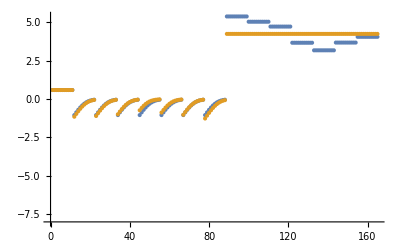

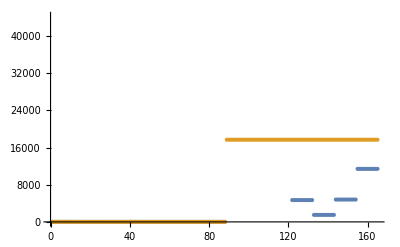

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

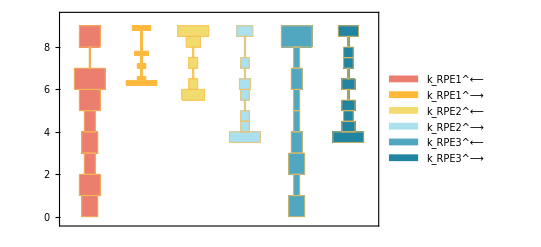

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

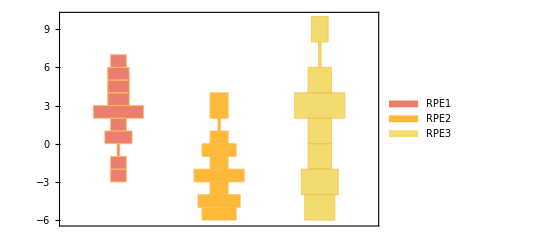

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

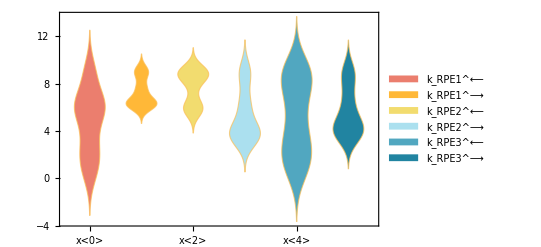

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

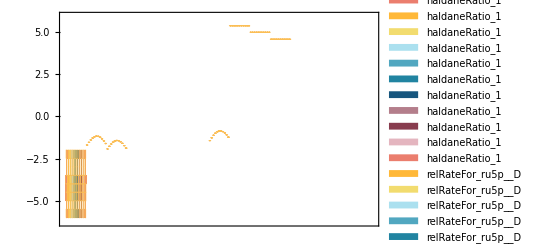

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

backCalculateKms[(ru5p__D^c⇌xu5p__D^c)^RPE,{{1,ru5p__D,0.0016,{0.0014,0.0018},{},M,8.5,23,{{glygly,0.05}},{{mg2,0.0069},{cl,0.0138}}},{1,ru5p__D,0.0018,{0.0017,0.0019},{},M,8.5,23,{{glygly,0.05}},{{mg2,0.0069},{cl,0.0138}}},{1,ru5p__D,0.0024,{0.002,0.0028},{},M,8.5,23,{{glygly,0.05}},{{mg2,0.0069},{cl,0.0138}}},{1,ru5p__D,0.0048,{0.0043,0.0053},{},M,8.5,23,{{glygly,0.05}},{{mg2,0.0069},{cl,0.0138}}},{1,ru5p__D,0.0032,{0.0029,0.0035},{},M,7.5,25,{{hepes,0.05}},{{mg2,0.01},{cl,0.02},{na1,0.05}}},{1,ru5p__D,0.0022,{0.0019,0.0025},{},M,7.5,25,{{hepes,0.05}},{{mg2,0.01},{cl,0.02},{na1,0.05}}},{1,ru5p__D,0.0012,{0.0011,0.0013},{},M,7.5,25,{{hepes,0.05}},{{mg2,0.01},{cl,0.02},{na1,0.05}}}},{(ru5p__D^c k_RPE1^⟶ (k_RPE2^⟶+k_RPE3^⟵+k_RPE3^⟶))/(k_RPE1^⟵ (k_RPE2^⟶+k_RPE3^⟵)+k_RPE2^⟶ k_RPE3^⟶+ru5p__D^c k_RPE1^⟶ (k_RPE2^⟶+k_RPE3^⟵+k_RPE3^⟶))},{(xu5p__D^c k_RPE2^⟵ (k_RPE1^⟵+k_RPE3^⟵+k_RPE3^⟶))/(k_RPE1^⟵ (k_RPE2^⟶+k_RPE3^⟵)+k_RPE2^⟶ k_RPE3^⟶+xu5p__D^c k_RPE2^⟵ (k_RPE1^⟵+k_RPE3^⟵+k_RPE3^⟶))},{ru5p__D^c→∞},{xu5p__D^c→∞},{k_RPE1^⟵→84316.8,k_RPE1^⟶→4.19196×10^7,k_RPE2^⟵→515212.,k_RPE2^⟶→733127.,k_RPE3^⟵→5.7006×10^6,k_RPE3^⟶→31425.9},1,RPE]

```mathematica
Print[relativeRateForward]
```

{(ru5p__D^c k_RPE1^⟶ (k_RPE2^⟶+k_RPE3^⟵+k_RPE3^⟶))/(k_RPE1^⟵ (k_RPE2^⟶+k_RPE3^⟵)+k_RPE2^⟶ k_RPE3^⟶+ru5p__D^c k_RPE1^⟶ (k_RPE2^⟶+k_RPE3^⟵+k_RPE3^⟶))}

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
241652. | 21337. | 91.1704
109645. | 21337. | 80.5399
53019.2 | 21337. | 59.7561
4688.77 | 21337. | 355.066
1501.41 | 21337. | 1321.14
4804.5 | 21337. | 344.105
11410.7 | 21337. | 86.9917

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
3.9 | 3.89999 | 0.000277191

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
3.9 | 3.89999 | 0.000277191

```mathematica
{{"data value", "predicted value", "error in %"}, {12.9, 12.900000000022317, 1.7299512382469261*^-10}}
```

{{data value,predicted value,error in %},{12.9,12.9,1.72995×10^-10}}

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKic[{{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/haldaneRatio_1.txt,12.9},{1,0,0.0000145,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.0909091},{1,0,0.000022981,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.136807},{1,0,0.0000364224,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.20076},{1,0,0.0000577255,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.284747},{1,0,0.0000914888,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.386863},{1,0,0.000145,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.5},{1,0,0.00022981,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.613137},{1,0,0.000364224,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.715253},{1,0,0.000577255,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.79924},{1,0,0.000914888,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.863193},{1,0,0.00145,0.00018,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_g6p.txt,0.909091},{1,0,0.001,1.5×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.0909091},{1,0,0.001,2.37734×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.136807},{1,0,0.001,3.76783×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.20076},{1,0,0.001,5.97161×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.284747},{1,0,0.001,9.46436×10^-6,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.386863},{1,0,0.001,0.000015,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.5},{1,0,0.001,0.0000237734,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.613137},{1,0,0.001,0.0000376783,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.715253},{1,0,0.001,0.0000597161,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.79924},{1,0,0.001,0.0000946436,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.863193},{1,0,0.001,0.00015,0,1,8,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_G6PDH2r_typeII/input/relRateFor_nadp.txt,0.909091}},{2.32837×10^-23,{0.021302,76.4848,0.000162378,0.000384575,399.883,7.02493×10^6,0.0196564,9115.38,5.44613×10^8,0.000101412},{12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,12.9,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091}},{Priority,6pgl[c],g6p[c],nadp[c],nadph[c],param_G6PDH2r_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

backCalculateKiu[{{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0,0,1,7.5,25,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/haldaneRatio_1.txt,0.443},{1,0.00011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.0909091},{1,0.000174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.136807},{1,0.000276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.20076},{1,0.000437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.284747},{1,0.000694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.386863},{1,0.0011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.5},{1,0.00174338,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.613137},{1,0.00276308,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.715253},{1,0.00437918,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.79924},{1,0.00694053,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.863193},{1,0.011,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/relRateFor_r5p.txt,0.909091},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.},{1,0.01,0,1,7.5,37,/Users/guest/Desktop/internship stuff/MASSef/examples/fit_RPIb_typeII/input/absRateFor.txt,52.}},{1.15461×10^-22,{538.263,26248.2,1.50533×10^8,28.8607,194.069,9.19561×10^6},{0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.443,0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.,52.}},{Priority,r5p[c],ru5p__D[c],param_RPIb_total,param_pH,param_Temp,FileFlag,Target_Data},{}]

#### Export rate back calculated parameter error distribution

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

Set::shape: Lists {predictedParameters,predictedParameterErrors} and exportPredictedParametersAndErrors[(ru5p__D^c⇌xu5p__D^c)^RPE,RPE,«20»,{Priority,ru5p__D[c],xu5p__D[c],param_RPE_total,param_pH,param_Temp,FileFlag,Target_Data}] are not the same shape.

Part::take: Cannot take positions 3 through -1 in predictedParameterErrors.

Part::partd: Part specification predictedParameterErrors⟦1⟧ is longer than depth of object.

BoxWhiskerChart::ldata: Transpose[predictedParameterErrors⟦3;;All⟧] is not a valid dataset or list of datasets.

BoxWhiskerChart[Transpose[predictedParameterErrors⟦3;;All⟧],ChartLabels→{predictedParameterErrors⟦1⟧}]